# ezARPACK unit tests

## Symmetric matrices

```mathematica
(* Matrix size *)
Nmat=100;

(* Parameters of matrix A *)
diagcoeffshift=-0.55;
diagcoeffamp=1.0;
offdiagoffset=3;
offdiagcoeff=-1.05;

(* Matrix A *)
A=Table[If[i==j,diagcoeffamp*Mod[(i-1),2]+diagcoeffshift,If[Abs[i-j]==offdiagoffset,offdiagcoeff,0]],{i,1,Nmat},{j,1,Nmat}];
Simplify[Det[A]≠0]

(* Matrix M *)
M=Table[If[i==j,1.5,If[Abs[i-j]==1,0.25,0]],{i,1,Nmat},{j,1,Nmat}];
Positive@Min@Eigenvalues[M]
```

True

True

### Standard eigenproblem

```mathematica
(* Requested number of eigenvalues *)
nev=10;

eig=Eigenvalues[A];

(* Smallest *)
Sort[Sort[eig,#1<#2&][[1;;nev]]]
(* Largest *)
Sort[Sort[eig,#1>#2&][[1;;nev]]]
(* SmallestMagnitude *)
Sort[Sort[eig,Abs[#1]<Abs[#2]&][[1;;nev]]]
(* LargestMagnitude *)
Sort[Sort[eig,Abs[#1]>Abs[#2]&][[1;;nev]]]
(* BothEnds *)
Sort[Join[Sort[eig][[1;;nev/2]],Sort[eig][[-nev/2;;-1]]]]
```

{-2.20048,-2.19999,-2.19999,-2.17589,-2.17394,-2.17394,-2.13516,-2.1308,-2.1308,-2.07868}

{1.97868,2.0308,2.0308,2.03516,2.07394,2.07394,2.07589,2.09999,2.09999,2.10048}

{-0.586232,-0.558799,-0.55,0.45,0.458799,0.486232,0.486232,0.523988,0.581584,0.581584}

{-2.20048,-2.19999,-2.19999,-2.17589,-2.17394,-2.17394,-2.13516,-2.1308,-2.1308,2.10048}

{-2.20048,-2.19999,-2.19999,-2.17589,-2.17394,2.07394,2.07589,2.09999,2.09999,2.10048}

### Generalized eigenproblem : invert mode

```mathematica
(* Requested number of eigenvalues *)
nev=10;

eig=Eigenvalues[{A,M}];

(* Smallest *)
Sort[Sort[eig,#1<#2&][[1;;nev]]]
(* Largest *)
Sort[Sort[eig,#1>#2&][[1;;nev]]]
(* SmallestMagnitude *)
Sort[Sort[eig,Abs[#1]<Abs[#2]&][[1;;nev]]]
(* LargestMagnitude *)
Sort[Sort[eig,Abs[#1]>Abs[#2]&][[1;;nev]]]
(* BothEnds *)
Sort[Join[Sort[eig][[1;;nev/2]],Sort[eig][[-nev/2;;-1]]]]
```

{-1.76379,-1.76376,-1.74252,-1.74246,-1.70728,-1.70725,-1.65873,-1.65825,-1.59747,-1.5959}

{1.26456,1.40626,1.53935,1.66138,1.77058,1.86544,1.94475,2.00749,2.05286,2.08031}

{-0.377015,-0.373002,-0.369639,0.300001,0.306314,0.321686,0.325109,0.352211,0.376032,0.398084}

{-1.76379,-1.76376,-1.74252,-1.74246,1.77058,1.86544,1.94475,2.00749,2.05286,2.08031}

{-1.76379,-1.76376,-1.74252,-1.74246,-1.70728,1.86544,1.94475,2.00749,2.05286,2.08031}

### Generalized eigenproblem: Shift-and-Invert mode

```mathematica
(* Requested number of eigenvalues *)
nev=10;
(* Spectral shift *)
σ=2.0;

eig=Eigenvalues[Inverse[A-σ M].M];
SpectralTransform[ν_]:=σ+1/ν;

(* Smallest *)
Sort[SpectralTransform[Sort[eig,#1<#2&][[;;nev]]]]
(* Largest *)
Sort[SpectralTransform[Sort[eig,#1>#2&][[;;nev]]]]
(* SmallestMagnitude *)
Sort[SpectralTransform[Sort[eig,Abs[#1]<Abs[#2]&][[;;nev]]]]
(* LargestMagnitude *)
Sort[SpectralTransform[Sort[eig,Abs[#1]>Abs[#2]&][[;;nev]]]]
(* BothEnds *)
BothEnds[l_]:=Join[l[[1;;nev/2]],l[[-nev/2;;-1]]];
Sort[SpectralTransform[BothEnds[Sort[eig]]]]
```

{1.1958,1.20967,1.20977,1.26456,1.40626,1.53935,1.66138,1.77058,1.86544,1.94475}

{-1.76379,-1.76376,-1.74252,-1.74246,-1.70728,-1.70725,-1.65873,2.00749,2.05286,2.08031}

{-1.76379,-1.76376,-1.74252,-1.74246,-1.70728,-1.70725,-1.65873,-1.65825,-1.59747,-1.5959}

{1.26456,1.40626,1.53935,1.66138,1.77058,1.86544,1.94475,2.00749,2.05286,2.08031}

{-1.76379,-1.76376,1.53935,1.66138,1.77058,1.86544,1.94475,2.00749,2.05286,2.08031}

### Generalized eigenproblem: Buckling mode

```mathematica
(* Requested number of eigenvalues *)
nev=10;
(* Spectral shift *)
σ=3.3;

K=M;
KG=A;

eig=Eigenvalues[Inverse[K-σ KG].K];
SpectralTransform[ν_]:=σ/(1-1/ν);

(* Smallest *)
Sort[SpectralTransform[Sort[eig,#1<#2&][[;;nev]]]]
(* Largest *)
Sort[SpectralTransform[Sort[eig,#1>#2&][[;;nev]]]]
(* SmallestMagnitude *)
Sort[SpectralTransform[Sort[eig,Abs[#1]<Abs[#2]&][[;;nev]]]]
(* LargestMagnitude *)
Sort[SpectralTransform[Sort[eig,Abs[#1]>Abs[#2]&][[;;nev]]]]
(* BothEnds *)
BothEnds[l_]:=Join[l[[1;;nev/2]],l[[-nev/2;;-1]]];
Sort[SpectralTransform[BothEnds[Sort[eig]]]]
```

{1.94686,1.96744,2.23282,2.34381,2.51203,2.65935,2.8392,3.07589,3.10862,3.26463}

{-2.70534,-2.68095,-2.65242,-2.47667,-2.38063,-2.30079,-2.16154,-2.00429,-1.8836,3.33333}

{-0.626607,-0.625989,-0.603045,-0.602872,-0.585736,-0.585727,-0.573903,-0.573881,-0.56697,-0.566961}

{1.96744,2.23282,2.34381,2.51203,2.65935,2.8392,3.07589,3.10862,3.26463,3.33333}

{-2.70534,-2.68095,-2.65242,-2.47667,2.65935,2.8392,3.07589,3.10862,3.26463,3.33333}

### Generalized eigenproblem: Cayley transformed mode

```mathematica
(* Requested number of eigenvalues *)
nev=10;
(* Spectral shift *)
σ=2.0;

eig=Eigenvalues[Inverse[A-σ M].(A+σ M)];
SpectralTransform[ν_]:=σ(ν+1)/(ν-1);

(* Smallest *)
Sort[SpectralTransform[Sort[eig,#1<#2&][[;;nev]]]]
(* Largest *)
Sort[SpectralTransform[Sort[eig,#1>#2&][[;;nev]]]]
(* SmallestMagnitude *)
Sort[SpectralTransform[Sort[eig,Abs[#1]<Abs[#2]&][[;;nev]]]]
(* LargestMagnitude *)
Sort[SpectralTransform[Sort[eig,Abs[#1]>Abs[#2]&][[;;nev]]]]
(* BothEnds *)
BothEnds[l_]:=Join[l[[1;;nev/2]],l[[-nev/2;;-1]]];
Sort[SpectralTransform[BothEnds[Sort[eig]]]]
```

{1.1958,1.20967,1.20977,1.26456,1.40626,1.53935,1.66138,1.77058,1.86544,1.94475}

{-1.76379,-1.76376,-1.74252,-1.74246,-1.70728,-1.70725,-1.65873,2.00749,2.05286,2.08031}

{-1.76379,-1.76376,-1.74252,-1.74246,-1.70728,-1.70725,-1.65873,-1.65825,-1.59747,-1.5959}

{1.26456,1.40626,1.53935,1.66138,1.77058,1.86544,1.94475,2.00749,2.05286,2.08031}

{-1.76379,-1.76376,1.53935,1.66138,1.77058,1.86544,1.94475,2.00749,2.05286,2.08031}

## Asymmetric matrices

```mathematica
(* Matrix size *)
Nmat=100;

(* Parameters of matrix A *)
diagcoeffshift=-0.55;
diagcoeffamp=1.0;
offdiagoffset=3;
offdiagcoeff=-1.05;

(* Matrix A *)
A=Table[Piecewise[{
{diagcoeffamp*Mod[(i-1),2]+diagcoeffshift,i==j},
{offdiagcoeff,j-i==offdiagoffset},
{-offdiagcoeff,i-j==offdiagoffset}
}],{i,1,Nmat},{j,1,Nmat}];
Simplify[Det[A]≠0]

(* Matrix M *)
M=Table[If[i==j,1.5,If[Abs[i-j]==1,0.25,0]],{i,1,Nmat},{j,1,Nmat}];
Positive@Min@Eigenvalues[M]
```

True

True

### Standard eigenproblem

```mathematica
(* Requested number of eigenvalues *)
nev=10;

eig=Eigenvalues[A];

(* LargestMagnitude *)
Sort[eig,Abs[#1]>Abs[#2]&][[1;;nev]]
(* SmallestMagnitude *)
Sort[eig,Abs[#1]<Abs[#2]&][[1;;nev]]
(* LargestReal *)
Sort[eig,Abs[Re[#1]]>Abs[Re[#2]]&][[1;;nev]]
(* SmallestReal *)
Sort[eig,Abs[Re[#1]]<Abs[Re[#2]]&][[1;;nev]]
(* LargestImag *)
Sort[eig,Abs[Im[#1]]>Abs[Im[#2]]&][[1;;nev]]
(* SmallestImag *)
Sort[eig,Abs[Im[#1]]<Abs[Im[#2]]&][[1;;nev]]
```

{-0.05-2.0309 ⅈ,-0.05+2.0309 ⅈ,-0.05-2.03038 ⅈ,-0.05+2.03038 ⅈ,-0.05-2.03038 ⅈ,-0.05+2.03038 ⅈ,-0.05-2.00484 ⅈ,-0.05+2.00484 ⅈ,-0.05-2.00277 ⅈ,-0.05+2.00277 ⅈ}

{0.127866+0. ⅈ,-0.227866+0. ⅈ,0.267964+0. ⅈ,0.267964+0. ⅈ,-0.05-0.283322 ⅈ,-0.05+0.283322 ⅈ,-0.05-0.283322 ⅈ,-0.05+0.283322 ⅈ,0.362963+0. ⅈ,-0.367964+0. ⅈ}

{-0.55+0. ⅈ,-0.541043+0. ⅈ,-0.510929+0. ⅈ,-0.510929+0. ⅈ,-0.462963+0. ⅈ,0.45+0. ⅈ,0.441043+0. ⅈ,0.410929+0. ⅈ,0.410929+0. ⅈ,-0.367964+0. ⅈ}

{-0.05-1.95697 ⅈ,-0.05+1.95697 ⅈ,-0.05-0.283322 ⅈ,-0.05+0.283322 ⅈ,-0.05-0.570513 ⅈ,-0.05+0.570513 ⅈ,-0.05-0.656663 ⅈ,-0.05+0.656663 ⅈ,-0.05-0.791322 ⅈ,-0.05+0.791322 ⅈ}

{-0.05-2.0309 ⅈ,-0.05+2.0309 ⅈ,-0.05-2.03038 ⅈ,-0.05+2.03038 ⅈ,-0.05-2.03038 ⅈ,-0.05+2.03038 ⅈ,-0.05-2.00484 ⅈ,-0.05+2.00484 ⅈ,-0.05-2.00277 ⅈ,-0.05+2.00277 ⅈ}

{0.127866+0. ⅈ,-0.227866+0. ⅈ,0.267964+0. ⅈ,0.267964+0. ⅈ,0.362963+0. ⅈ,-0.367964+0. ⅈ,-0.367964+0. ⅈ,0.410929+0. ⅈ,0.410929+0. ⅈ,0.441043+0. ⅈ}

### Generalized eigenproblem : invert mode

```mathematica
(* Requested number of eigenvalues *)
nev=10;

eig=Eigenvalues[Inverse[M].A];

(* LargestMagnitude *)
Sort[eig,Abs[#1]>Abs[#2]&][[1;;nev]]
(* SmallestMagnitude *)
Sort[eig,Abs[#1]<Abs[#2]&][[1;;nev]]
(* LargestReal *)
Sort[eig,Abs[Re[#1]]>Abs[Re[#2]]&][[1;;nev]]
(* SmallestReal *)
Sort[eig,Abs[Re[#1]]<Abs[Re[#2]]&][[1;;nev]]
(* LargestImag *)
Sort[eig,Abs[Im[#1]]>Abs[Im[#2]]&][[1;;nev]]
(* SmallestImag *)
Sort[eig,Abs[Im[#1]]<Abs[Im[#2]]&][[1;;nev]]
```

{-0.0474073-1.92472 ⅈ,-0.0474073+1.92472 ⅈ,-0.0473838-1.89814 ⅈ,-0.0473838+1.89814 ⅈ,-0.0473452-1.85414 ⅈ,-0.0473452+1.85414 ⅈ,-0.0472921-1.79314 ⅈ,-0.0472921+1.79314 ⅈ,-0.0472252-1.71574 ⅈ,-0.0472252+1.71574 ⅈ}

{0.0919172+0. ⅈ,-0.0227763-0.133882 ⅈ,-0.0227763+0.133882 ⅈ,-0.172279+0. ⅈ,0.168875-0.0393753 ⅈ,0.168875+0.0393753 ⅈ,-0.035227-0.231504 ⅈ,-0.035227+0.231504 ⅈ,-0.231319-0.0616964 ⅈ,-0.231319+0.0616964 ⅈ}

{-0.376017+0. ⅈ,-0.361588+0. ⅈ,-0.345295-0.0329472 ⅈ,-0.345295+0.0329472 ⅈ,-0.31642+0. ⅈ,0.305718+0. ⅈ,0.294738+0. ⅈ,0.275674-0.0247001 ⅈ,0.275674+0.0247001 ⅈ,0.247855+0. ⅈ}

{-0.0227763-0.133882 ⅈ,-0.0227763+0.133882 ⅈ,-0.0256428-1.04258 ⅈ,-0.0256428+1.04258 ⅈ,-0.0256732-1.02869 ⅈ,-0.0256732+1.02869 ⅈ,-0.0258295-0.974049 ⅈ,-0.0258295+0.974049 ⅈ,-0.0260127-0.50794 ⅈ,-0.0260127+0.50794 ⅈ}

{-0.0474073-1.92472 ⅈ,-0.0474073+1.92472 ⅈ,-0.0473838-1.89814 ⅈ,-0.0473838+1.89814 ⅈ,-0.0473452-1.85414 ⅈ,-0.0473452+1.85414 ⅈ,-0.0472921-1.79314 ⅈ,-0.0472921+1.79314 ⅈ,-0.0472252-1.71574 ⅈ,-0.0472252+1.71574 ⅈ}

{0.0919172+0. ⅈ,-0.172279+0. ⅈ,0.247855+0. ⅈ,0.294738+0. ⅈ,0.305718+0. ⅈ,-0.31642+0. ⅈ,-0.361588+0. ⅈ,-0.376017+0. ⅈ,0.275674-0.0247001 ⅈ,0.275674+0.0247001 ⅈ}

### Generalized eigenproblem : Shift-and-Invert mode

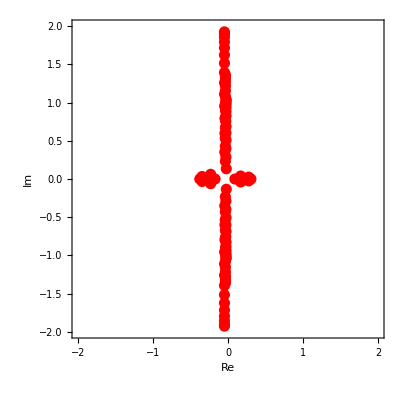

{-0.0474073-1.92472 ⅈ,-0.0474073+1.92472 ⅈ,-0.0473838-1.89814 ⅈ,-0.0473838+1.89814 ⅈ,-0.0473452+1.85414 ⅈ,-0.0473452-1.85414 ⅈ,-0.0472921+1.79314 ⅈ,-0.0472921-1.79314 ⅈ,-0.0472252+1.71574 ⅈ,-0.0472252-1.71574 ⅈ}

{0.305718+0. ⅈ,0.294738+0. ⅈ,0.275674+0.0247001 ⅈ,0.275674-0.0247001 ⅈ,0.247855+0. ⅈ,0.168875+0.0393753 ⅈ,0.168875-0.0393753 ⅈ,0.0919172+0. ⅈ,-0.0227763-0.133882 ⅈ,-0.0227763+0.133882 ⅈ}

{-0.0474073+1.92472 ⅈ,-0.0473838+1.89814 ⅈ,-0.0473452+1.85414 ⅈ,-0.0472921+1.79314 ⅈ,-0.0472252+1.71574 ⅈ,-0.0471455+1.62267 ⅈ,-0.0470516+1.51484 ⅈ,-0.0468994+1.3934 ⅈ,-0.0337556+1.36214 ⅈ,-0.0337938+1.3438 ⅈ}

```mathematica
(* Requested number of eigenvalues *)
nev=10;
(* Spectral shift *)
σ=0.5+ⅈ 0.5;

eig=Eigenvalues[{A,M}];

ListPlot[{Re[#],Im[#]}&/@eig,AxesOrigin->{0,0},PlotRange->{{-2,2},{-2,2}},ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->Directive[Red,PointSize[.02]]]

Sort[eig,Abs[#1]>Abs[#2]&][[1;;nev]]
Sort[eig,Re[#1]>Re[#2]&][[1;;nev]]
Sort[eig,Im[#1]>Im[#2]&][[1;;nev]]
```

## Complex matrices

```mathematica
(* Matrix size *)
Nmat=100;

(* Parameters of matrix A *)
diagcoeffshift=-0.55;
diagcoeffamp=1.0;
offdiagoffset=3;
offdiagcoeff=0.5+0.5ⅈ;

(* Matrix A *)
A=Table[Piecewise[{
{diagcoeffamp*Mod[(i-1),2]+diagcoeffshift,i==j},
{offdiagcoeff,j-i==offdiagoffset},
{-offdiagcoeff,i-j==offdiagoffset}
}],{i,1,Nmat},{j,1,Nmat}];
Simplify[Det[A]≠0]

(* Matrix M *)
M=Table[If[i==j,1.5,If[Abs[i-j]==1,0.25,0]],{i,1,Nmat},{j,1,Nmat}];
Positive@Min@Eigenvalues[M]
```

True

True

### Standard eigenproblem

```mathematica
(* Requested number of eigenvalues *)
nev=10;

eig=Eigenvalues[A];

(* LargestMagnitude *)
Sort[eig,Abs[#1]>Abs[#2]&][[1;;nev]]
(* SmallestMagnitude *)
Sort[eig,Abs[#1]<Abs[#2]&][[1;;nev]]
(* LargestReal *)
Sort[eig,Re[#1]>Re[#2]&][[1;;nev]]
(* SmallestReal *)
Sort[eig,Re[#1]<Re[#2]&][[1;;nev]]
(* LargestImag *)
Sort[eig,Im[#1]>Im[#2]&][[1;;nev]]
(* SmallestImag *)
Sort[eig,Im[#1]<Im[#2]&][[1;;nev]]
```

{-1.11057+0.935313 ⅈ,-1.11035+0.935059 ⅈ,-1.11035+0.935059 ⅈ,-1.09936+0.92258 ⅈ,-1.09847+0.921568 ⅈ,-1.09847+0.921568 ⅈ,-1.08082+0.90144 ⅈ,-1.07884+0.899175 ⅈ,-1.07884+0.899175 ⅈ,1.01057-0.935313 ⅈ}

{0.45-8.9734×10^-16 ⅈ,0.450016-0.00402558 ⅈ,0.450289-0.017017 ⅈ,0.450289-0.017017 ⅈ,0.45129-0.0359444 ⅈ,0.45446-0.0669308 ⅈ,0.45446-0.0669308 ⅈ,0.459362-0.0972109 ⅈ,0.470306-0.143937 ⅈ,0.470306-0.143937 ⅈ}

{1.01057-0.935313 ⅈ,1.01035-0.935059 ⅈ,1.01035-0.935059 ⅈ,0.999359-0.92258 ⅈ,0.998469-0.921568 ⅈ,0.998469-0.921568 ⅈ,0.980822-0.90144 ⅈ,0.978842-0.899175 ⅈ,0.978842-0.899175 ⅈ,0.955188-0.872011 ⅈ}

{-1.11057+0.935313 ⅈ,-1.11035+0.935059 ⅈ,-1.11035+0.935059 ⅈ,-1.09936+0.92258 ⅈ,-1.09847+0.921568 ⅈ,-1.09847+0.921568 ⅈ,-1.08082+0.90144 ⅈ,-1.07884+0.899175 ⅈ,-1.07884+0.899175 ⅈ,-1.05519+0.872011 ⅈ}

{-1.11057+0.935313 ⅈ,-1.11035+0.935059 ⅈ,-1.11035+0.935059 ⅈ,-1.09936+0.92258 ⅈ,-1.09847+0.921568 ⅈ,-1.09847+0.921568 ⅈ,-1.08082+0.90144 ⅈ,-1.07884+0.899175 ⅈ,-1.07884+0.899175 ⅈ,-1.05519+0.872011 ⅈ}

{1.01057-0.935313 ⅈ,1.01035-0.935059 ⅈ,1.01035-0.935059 ⅈ,0.999359-0.92258 ⅈ,0.998469-0.921568 ⅈ,0.998469-0.921568 ⅈ,0.980822-0.90144 ⅈ,0.978842-0.899175 ⅈ,0.978842-0.899175 ⅈ,0.955188-0.872011 ⅈ}

### Generalized eigenproblem : invert mode

```mathematica
(* Requested number of eigenvalues *)
nev=10;

eig=Eigenvalues[Inverse[M].A];

(* LargestMagnitude *)
Sort[eig,Abs[#1]>Abs[#2]&][[1;;nev]]
(* SmallestMagnitude *)
Sort[eig,Abs[#1]<Abs[#2]&][[1;;nev]]
(* LargestReal *)
Sort[eig,Re[#1]>Re[#2]&][[1;;nev]]
(* SmallestReal *)
Sort[eig,Re[#1]<Re[#2]&][[1;;nev]]
(* LargestImag *)
Sort[eig,Im[#1]>Im[#2]&][[1;;nev]]
(* SmallestImag *)
Sort[eig,Im[#1]<Im[#2]&][[1;;nev]]
```

{-1.02599+0.895729 ⅈ,-1.01413+0.882856 ⅈ,-0.994544+0.861533 ⅈ,0.931848-0.894525 ⅈ,-0.96751+0.831957 ⅈ,0.920057-0.881624 ⅈ,0.900586-0.860251 ⅈ,-0.933409+0.794398 ⅈ,0.873709-0.830602 ⅈ,-0.892753+0.749197 ⅈ}

{0.285823-0.0207644 ⅈ,0.284505-0.0608005 ⅈ,0.295297+0.000832582 ⅈ,0.300215-0.0022626 ⅈ,0.302084-0.0206209 ⅈ,0.307305-0.00198898 ⅈ,0.308085-0.0577207 ⅈ,0.294211-0.110339 ⅈ,0.319825-0.0317443 ⅈ,0.324131-0.109889 ⅈ}

{0.931848-0.894525 ⅈ,0.920057-0.881624 ⅈ,0.900586-0.860251 ⅈ,0.873709-0.830602 ⅈ,0.839818-0.792941 ⅈ,0.799428-0.747601 ⅈ,0.753197-0.694986 ⅈ,0.701978-0.63564 ⅈ,0.677616-0.627309 ⅈ,0.669758-0.618332 ⅈ}

{-1.02599+0.895729 ⅈ,-1.01413+0.882856 ⅈ,-0.994544+0.861533 ⅈ,-0.96751+0.831957 ⅈ,-0.933409+0.794398 ⅈ,-0.892753+0.749197 ⅈ,-0.846186+0.696765 ⅈ,-0.794514+0.637626 ⅈ,-0.745125+0.627307 ⅈ,-0.738467+0.572395 ⅈ}

{-1.02599+0.895729 ⅈ,-1.01413+0.882856 ⅈ,-0.994544+0.861533 ⅈ,-0.96751+0.831957 ⅈ,-0.933409+0.794398 ⅈ,-0.892753+0.749197 ⅈ,-0.846186+0.696765 ⅈ,-0.794514+0.637626 ⅈ,-0.745125+0.627307 ⅈ,-0.737293+0.618343 ⅈ}

{0.931848-0.894525 ⅈ,0.920057-0.881624 ⅈ,0.900586-0.860251 ⅈ,0.873709-0.830602 ⅈ,0.839818-0.792941 ⅈ,0.799428-0.747601 ⅈ,0.753197-0.694986 ⅈ,0.701978-0.63564 ⅈ,0.677616-0.627309 ⅈ,0.669758-0.618332 ⅈ}

### Generalized eigenproblem: Shift-and-Invert mode

```mathematica
(* Requested number of eigenvalues *)
nev=10;
(* Spectral shift *)
σ=-1+0.9ⅈ;

eig=Eigenvalues[Inverse[A-σ M].M];
SpectralTransform[ν_]:=σ+1/ν;

(* LargestMagnitude *)
SpectralTransform[Sort[eig,Abs[#1]>Abs[#2]&][[1;;nev]]]
(* SmallestMagnitude *)
SpectralTransform[Sort[eig,Abs[#1]<Abs[#2]&][[1;;nev]]]
(* LargestReal *)
SpectralTransform[Sort[eig,Re[#1]>Re[#2]&][[1;;nev]]]
(* SmallestReal *)
SpectralTransform[Sort[eig,Re[#1]<Re[#2]&][[1;;nev]]]
(* LargestImag *)
SpectralTransform[Sort[eig,Im[#1]>Im[#2]&][[1;;nev]]]
(* SmallestImag *)
SpectralTransform[Sort[eig,Im[#1]<Im[#2]&][[1;;nev]]]
```

{-1.01413+0.882856 ⅈ,-1.02599+0.895729 ⅈ,-0.994544+0.861533 ⅈ,-0.96751+0.831957 ⅈ,-0.933409+0.794398 ⅈ,-0.892753+0.749197 ⅈ,-0.846186+0.696765 ⅈ,-0.794514+0.637626 ⅈ,-0.745125+0.627307 ⅈ,-0.737293+0.618343 ⅈ}

{0.931848-0.894525 ⅈ,0.920057-0.881624 ⅈ,0.900586-0.860251 ⅈ,0.873709-0.830602 ⅈ,0.839818-0.792941 ⅈ,0.799428-0.747601 ⅈ,0.753197-0.694986 ⅈ,0.701978-0.63564 ⅈ,0.677616-0.627309 ⅈ,0.669758-0.618332 ⅈ}

{-0.96751+0.831957 ⅈ,-0.933409+0.794398 ⅈ,-0.994544+0.861533 ⅈ,-0.892753+0.749197 ⅈ,-0.846186+0.696765 ⅈ,-0.794514+0.637626 ⅈ,-0.745125+0.627307 ⅈ,-0.737293+0.618343 ⅈ,-0.724479+0.603555 ⅈ,-0.706409+0.582924 ⅈ}

{-1.02599+0.895729 ⅈ,-1.01413+0.882856 ⅈ,0.931848-0.894525 ⅈ,0.920057-0.881624 ⅈ,0.900586-0.860251 ⅈ,0.873709-0.830602 ⅈ,0.839818-0.792941 ⅈ,0.799428-0.747601 ⅈ,0.753197-0.694986 ⅈ,0.701978-0.63564 ⅈ}

{-1.01413+0.882856 ⅈ,-0.994544+0.861533 ⅈ,-0.96751+0.831957 ⅈ,-0.933409+0.794398 ⅈ,-1.02599+0.895729 ⅈ,-0.892753+0.749197 ⅈ,-0.846186+0.696765 ⅈ,-0.794514+0.637626 ⅈ,-0.745125+0.627307 ⅈ,-0.737293+0.618343 ⅈ}

{0.931848-0.894525 ⅈ,0.920057-0.881624 ⅈ,0.900586-0.860251 ⅈ,0.873709-0.830602 ⅈ,0.839818-0.792941 ⅈ,0.799428-0.747601 ⅈ,0.753197-0.694986 ⅈ,0.701978-0.63564 ⅈ,0.677616-0.627309 ⅈ,0.669758-0.618332 ⅈ}